```mathematica
Needs["ClusterIntegration`"]
```

```mathematica
LaunchKernels[PBS["localhost",12,{"EnginePath"->"/usr/physics/torque","KernelProgram"->"/usr/physics/mathematica/math11.3/Executables/math","ToQueue"->True,"QueueName"->"physics","BatchCommand"->"#!/bin/csh \n #PBS -q physics -l nodes=node10:ppn=1 -l walltime=2400:00:00 -j oe -o /dev/null -N mathematica -V \n `mathkernel`"}]]
```

{KernelObject[109,localhost],KernelObject[110,localhost],KernelObject[111,localhost],KernelObject[112,localhost],KernelObject[113,localhost],KernelObject[114,localhost],KernelObject[115,localhost],KernelObject[116,localhost],KernelObject[117,localhost],KernelObject[118,localhost],KernelObject[119,localhost],KernelObject[120,localhost]}

```mathematica
ParallelEvaluate[Off[NIntegrate::zeroregion,NIntegrate::inumr,NIntegrate::ncvb,NIntegrate::slwcon,General::munfl,Power::infy,Infinity::indet,NIntegrate::izero,StableDistribution::posprm]];
```

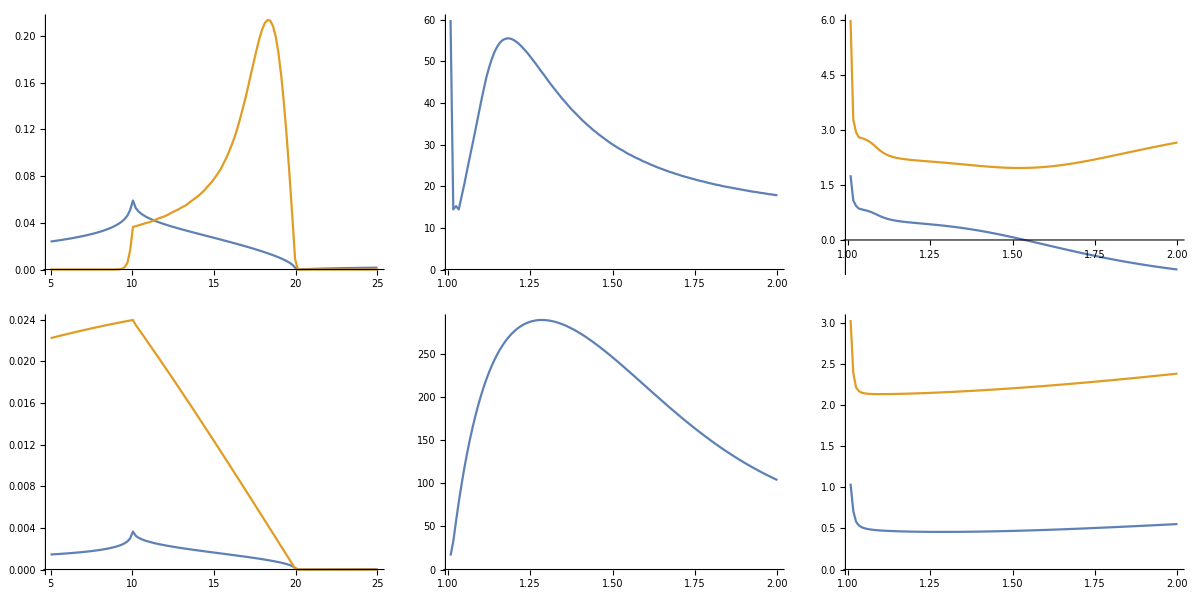

```mathematica
Grid@Table[With[{parset=P0params/.{(J->_)->(J->Jvar)},alphaset=R[1+1/120,2,120],alphaindex={24,-1}},With[{params=ParallelMap[ν0params[parset/.{(α->_)->(α->#)},0,500,0.1]&,alphaset]},{ListLinePlot[#,PlotRange->All]}&@Table[ParallelMap[{#,P0[#,μ,σ,α,β,d,Vr,θ,τ,ν,τrp]}&//.p,R[5,25,120]],{p,params[[alphaindex]]}]~Join~{ListLinePlot[Map[ν/.#&,params],PlotRange->All,DataRange->alphaset[[{1,-1}]]],ListLinePlot[Transpose[Table[NSM[{3,4},15,-5,5,120,P0[#,μ,σ,α,β,d,Vr,θ,τ,ν,τrp]&//.p],{p,params}]],DataRange->alphaset[[{1,-1}]]]}]],{Jvar,{0.02,0.2}}]
```

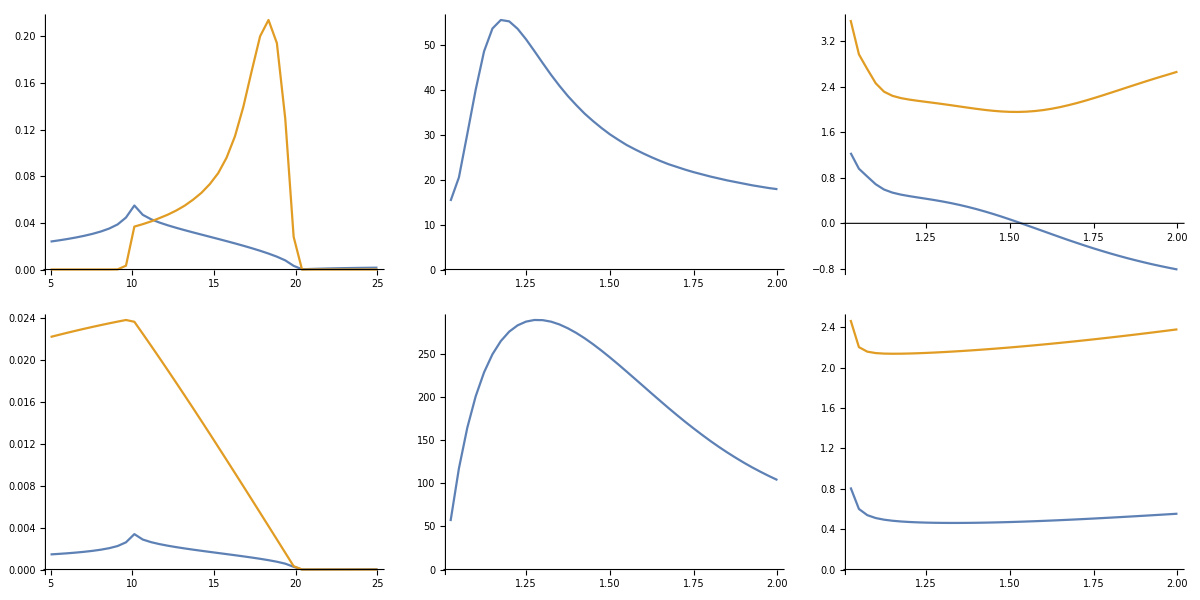

```mathematica
Grid@Table[With[{parset=P0params/.{(J->_)->(J->Jvar)},alphaset=R[1+1/40,2,40],alphaindex={8,-1}},With[{params=ParallelMap[ν0params[parset/.{(α->_)->(α->#)},0,500,0.1]&,alphaset]},{ListLinePlot[#,PlotRange->All]}&@Table[ParallelMap[{#,P0[#,μ,σ,α,β,d,Vr,θ,τ,ν,τrp]}&//.p,R[5,25,40]],{p,params[[alphaindex]]}]~Join~{ListLinePlot[Map[ν/.#&,params],PlotRange->All,DataRange->alphaset[[{1,-1}]]],ListLinePlot[Transpose[Table[NSM[{3,4},15,-5,5,40,P0[#,μ,σ,α,β,d,Vr,θ,τ,ν,τrp]&//.p],{p,params}]],DataRange->alphaset[[{1,-1}]]]}]],{Jvar,{0.02,0.2}}]
```